# tapered fiber “imaging”

Image with a point grey camera of a focused beam (633 fiber -> f=8 mm asphere -> f=3.1 mm asphere, to get roughly 2 micron spot). I think the fiber core size for the fiber may be the reason for the spot size being too large below. Also, the asphere box was labeled “very bad”

```mathematica
img=-Graphics-;
data=ImageData[(*ColorConvert[*)img(*,"Grayscale"]*)][[;;,;;,1]];
{ydim,xdim}=data//Dimensions
```

{960,1280}

```mathematica
pixPerMicron=12.12;
```

```mathematica
img
```

-Graphics-

```mathematica
xmicrons=Range[0,(xdim-1)/pixPerMicron,1/pixPerMicron];
xmicrons//Length
```

1280

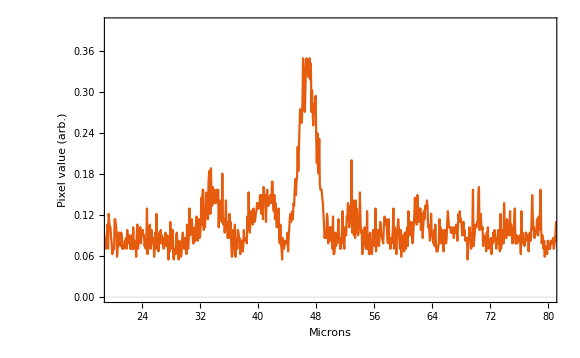

```mathematica
ListPlot[Transpose@{xmicrons,data[[382]]},Joined->True,PlotRange->{{20,80},{0,0.4}},PlotTheme->"Scientific",FrameLabel->{"Microns","Pixel value (arb.)"}]
```

```mathematica
Show[Image[data],Frame->True,FrameTicks->True,Ticks->{Table[{i,2*i},{i,Range[1,xdim,500]}],Table[{j,2*j},{j,Range[1,ydim,500]}]}]
```

-Graphics-

Image with a point grey camera + 8 mm asphere (the Urban camera) of a focused beam (633 fiber -> f=8 mm asphere -> 10x beam expander -> 0.4 NA JenOptik to get a roughly 2 micron spot).

```mathematica
img=-Graphics-;
data=ImageData[(*ColorConvert[*)img(*,"Grayscale"]*)][[;;,;;,1]];
data/=Max[data];
{ydim,xdim}=data//Dimensions
```

{960,1280}

```mathematica
Image[data[[400;;550,425;;575]]]
```

-Graphics-

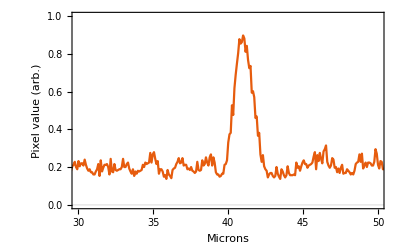

```mathematica
pixPerMicron=12.12;
xmicrons=Range[0,(xdim-1)/pixPerMicron,1/pixPerMicron];
ymicrons=Range[0,(ydim-1)/pixPerMicron,1/pixPerMicron];
ListPlot[Transpose@{xmicrons,data[[482]]},Joined->True,PlotRange->{{30,50},{0,1}},PlotTheme->"Scientific",FrameLabel->{"Microns","Pixel value (arb.)"}]
```

```mathematica
ymicrons[[-1]]
```

79.1254

```mathematica
data//Dimensions
```

{960,1280}

```mathematica
ymicrons//Length
```

960

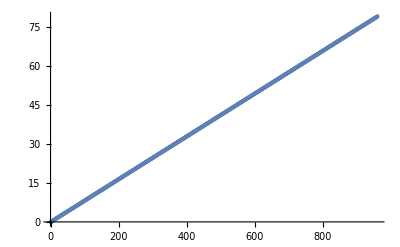

```mathematica
ListPlot[ymicrons]
```

```mathematica
xyf=Flatten[Array[{xmicrons[[#2]],ymicrons[[#1]],data[[400+#1,425+#2]]}&,data[[400;;550,425;;575]]//Dimensions],1];
Image[data[[400;;550,425;;575]]]
```

-Graphics-

```mathematica
xmicrons[[425]]-xmicrons[[575]]
ymicrons[[400]]-ymicrons[[550]]
```

-12.3762

-12.3762

```mathematica
ListPlot3D[xyf,PlotRange->{0,1},AxesLabel->{"x","y","f"}]
```

-Graphics3D-

```mathematica
model=a Exp[(-2(x-x0)^2)/wx^2]Exp[(-2(y-y0)^2)/wy^2];
fit=FindFit[xyf,model,{{a,0.9},{wx,2},{wy,2},{x0,6},{y0,6.5}},{x,y}]
```

{a→0.243829,wx→21.1937,wy→19.9675,x0→6.39547,y0→6.53544}

```mathematica
Plot3D[a Exp[(-2(x-x0)^2)/wx^2]Exp[(-2(y-y0)^2)/wy^2]/.{a->1,wx->1,wy->1,x0->6.395471826750817,y0->6.535445009759205},{x,0,12},{y,0,12},PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Plot3D[model/.fit,{x,0,12},{y,0,12},PlotRange->{0,1}]
```

-Graphics3D-